# The Music of the (Point-Like) Spheres

## Feynman Diagrams and Serialism

Silas Kurt Grossberndt

	In the fields of particle physics and music theory, the number 12 is fundamental. For music, there are 12 tones to the chromatic scale (in the western tradition) and, in particle physics, there are 12 fundamental fermions; just as Feynman diagrams are to be rotated and remain valid, musicians from the second Viennese school, such as Schoenberg, defined matrices to  give similar rotations on 12-tone music. Particle physics is hard to understand, and often written in the intractable, to the general public, code of Feynman diagrams. Further, physics is often accused of failing to recognize the beauty and art of the world, reducing mystery to mathematical equations. Thus, it would be of interest to represent particle interactions and Feynman diagrams in a musical manner.

## Feynman Diagrams and Particle Physics

Feynman diagrams are powerful tool of particle physics that allows for the pictoral representation of particle interactions. These tools show the progress of an interaction, with time on one axis (usually the vertical for a small diagram--as is shown on the electron positron interaction below-- and horizontal for large interactions--seen on the Higgs decay below).  Further, the Feynman diagrams have the property that topological deformations of a valid Feynman diagram are still valid Feynman diagrams.

## Naïve First Mapping

However, to just assign random notes to the particles would create a cacophony.To display this issue, let us assign the twelve tones as below

Particle | Tone
up (u) | A
down (d) | B♭
charm (c) | B
strange (s) | C
top (t) | C♯
bottom (b) | D
electron (e^-) | E♭
muon (μ^-) | E
tau (τ^-) | F
electron neutrino (ν_e) | F♯
muon neutrino (ν_μ) | G
tau neutrino (ν_τ) | G♯

Now, the bosons must be added to create any physical Feynman Diagram. While there is no clear way of performing this mapping, one can choose the photon (γ) to be the notes of the electron, muon and tau (E♭, E, F), the gluon as the notes of the quarks, selecting one group of three and another group of three to maintain a reasonable number of notes. To this end g_1 is up, charm, top (A, B, C♯) and g_2 is down, strange, bottom (B♭, C, D). Then, as the Higgs (H) coupling is dependent on mass, we select the particle family that has the highest (relative ) mass, i.e. top, bottom, tau and tau neutrino (C♯, D, F, A♭). Then, the  W^+are the three neutrinos shifted up by a half-step, W^- is the three neutrinos shifted down a half step and Z^0 is the bare three neutrinos--(G, A♭, A), (F, F♯, G) and (F♯, G, G♯) respectively. In regards to the anti-particles (for example μ^+ or ū), they shall be dealt with by way of the sixth (minor to the base note). This method of mapping will be carried through in the remainder of this work, as it is strongly based in physical reasoning. Consider the following interactions (electron-positron scattering and Higgs decay through the bottom quark channel, where the Higgs is produced by Gluon Fusion, although understanding such processes are not relevant to the discussion).

```mathematica
-Graphics--Graphics-
```

Then, the musical equivalents of these are:

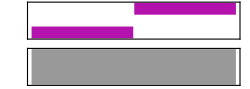
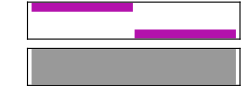
```mathematica
eantieinteraction=Sound[{Ds[3], Cn[3]}, 6]+ Pause[1]+{EmitSound[Ds[6]]+EmitSound[En[6]]+EmitSound[Fn[6]]}+Pause[1]+ Sound[{Cn[3], Dn[3]}, 6]
{-Graphics-+-Graphics-+5 Null}
Button["Electron Positron Interaction",eantieinteraction]
```

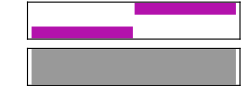
{-Graphics-+-Graphics-+5 Null}

{-Graphics-+-Graphics-+5 Null}

Electron Positron Interaction

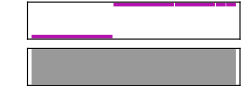
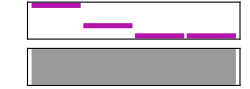
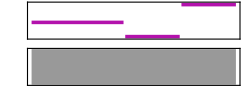
```mathematica
higgsDecay=EmitSound[An]+EmitSound[Bn]+EmitSound[Cs]+Pause[1]+EmitSound[As]+EmitSound[Cn]+EmitSound[Dn]+Pause[1]+Sound[{Fn[5], Cs[3], As[3]}, 6]+ Pause[1]+ EmitSound[Cs]+EmitSound[Dn]+EmitSound[Fn]+EmitSound[Gs]+Pause[1]+Sound[{Dn[4], Bn[3], Bn[2], Bn[0.5], Bn[0.5]}]+Pause[1]+EmitSound[Gn]+EmitSound[An]+EmitSound[Gs]+Pause[0.5]+EmitSound[Fn]+EmitSound[Fs]+EmitSound[Gn]+Pause[1]+Sound[{As[1], Fs[1], En[1], En[1]}]
2 EmitSound[An]+EmitSound[As]+EmitSound[Bn]+EmitSound[Cn]+2 EmitSound[Cs]+2 EmitSound[Dn]+2 EmitSound[Fn]+EmitSound[Fs]+EmitSound[Gn]+EmitSound[Gn]+2 EmitSound[Gs]+-Graphics-+-Graphics-+-Graphics-+7 Null
Button["Higgs Decay", higgsDecay]
```

2 EmitSound[An]+EmitSound[As]+EmitSound[Bn]+EmitSound[Cn]+2 EmitSound[Cs]+2 EmitSound[Dn]+2 EmitSound[Fn]+EmitSound[Fs]+2 EmitSound[Gn]+2 EmitSound[Gs]+-Graphics-+-Graphics-+-Graphics-+7 Null

2 EmitSound[An]+EmitSound[As]+EmitSound[Bn]+EmitSound[Cn]+2 EmitSound[Cs]+2 EmitSound[Dn]+2 EmitSound[Fn]+EmitSound[Fs]+2 EmitSound[Gn]+2 EmitSound[Gs]+-Graphics-+-Graphics-+-Graphics-+7 Null

Higgs Decay

One notes that the music is hard to play for a string instrument and not particularly well motivated. There is no relation between the members of a generation, and the bosons are discordant. Thus, one is motivated to define a more careful mapping to reflect the interconnection of the fermions.

## A Careful Mapping and the Neutrino Problem

### Base Chords

In order to reflect the connection of the four particles in a generation, one would be motivated to utilize the major chords, a they are a simple relationship structure within music theory. However, the basic major chord only has three elements (the base note, the third and the fifth), but the next logical extension is to add on the seventh to form the major-seventh chord. These relationships are defined by the major scale, where each note is its position within the scale. For the C scale below, the major chord is C, E, G and the Seventh Major is C, E, G, B.

WolframAlphaQueryResults

C_4 | D_4 | E_4 | F_4 | G_4 | A_4 | B_4 | C_5

However, this mapping is not guaranteed to cover all 12 notes, thus leading to a non-bijective mapping, which is sub-optimal for composing music from the diagrams. Thus, it is necessary to define a mapping that fully covers all notes. To do this, we must define a rule that takes a base note and generates the major chord, and then add on the seventh, then map this rule thrice over on unique mappings (as A,B,C base notes is the same as B,C,A  and all other variations of such for purposes of complete coverage).

```mathematica
(*This is the rule for a single group/chord*)
NoNeut[l_]:={ChrS⟦l⟧, ChrS⟦Third[l]⟧, ChrS⟦Fifth[l]⟧};
(*This is the group of the nine fermions w/out neutrinos*)
BaseGroup[w_,x_, o_]={NoNeut[w], NoNeut[x], NoNeut[o]};
NotesLeftOver[p_, q_, r_]:=Complement[ChrS, Flatten[BaseGroup[p, q, r]]];
```

```mathematica
maxIndex=12;
tNotes=Table[NotesLeftOver[x,y,z], {x, 1,maxIndex-2}, {y, x+1, maxIndex-1}, {z, y+1, maxIndex}] //Flatten[#, 2]&;
indexofCandidates=Position[tNotes, {_,_,_}];
candidates=Extract[tNotes, indexofCandidates]
```

(Cn | Gn | Gs
Bn | Fs | Gn
As | Fn | Fs
An | Cs | Gs
An | As | Dn
As | Bn | Ds
Bn | Cn | En
Cn | Cs | Fn
Cs | Dn | Fs
Dn | Ds | Gn
Ds | En | Gs
An | En | Fn)

```mathematica
First@indexofCandidates
```

{1}

The above table gives all the unique sets of major chords, from which we select the candidate that maximally cover the space, i.e. those that cover nine of the 12 notes of the chromatic scale. This list of candidates are the remaining choices for the fourth particle of each generations, i.e. the neutrinos. The first index tells us that the  first candidate has Chords (A, B♭, B), thus the candidates have three mappings, where two are a set of  two diminished 7th’s and a diminished second (where diminished mans that the note is decreased down the scale by a half step), and another of two sixths and a diminished third. This is sub-optimal as this in not a consistent mapping.

### Seventh Chords

In order to evaluate all candidates and verify that the uniqueness is necessary, one attempts mappings of all of the options other then those already in the major chord (i.e. Diminished Second, Second, Diminished Third, Fourth, Diminished Fifth, Diminished Sixth, Sixth, Diminished Seventh, Seventh). Taking the Seventh, the distribution of the number of remaining notes is

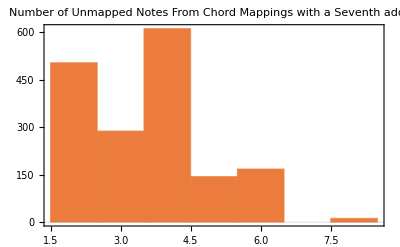

```mathematica
SeventhRule[s_]:={Flatten[NoNeut[s]], ChrS⟦Seventh[s]⟧};
NotesLeftfromS[t_, u_, v_]:=Complement[ChrS, Flatten[{SeventhRule[t], SeventhRule[u], SeventhRule[v]}]];
ProofofNoSeventh:=Array[NotesLeftfromS, {12, 12, 12}];
Seventhdata:=Flatten[ProofofNoSeventh,2];
Histogram[Length/@Seventhdata⟦1;;Length[Seventhdata]⟧,PlotTheme->"Scientific", PlotLabel->HoldForm[Number of Unmapped Notes From Chord  Mappings with a Seventh added] ]
```

Further, for unique elements, the distribution becomes

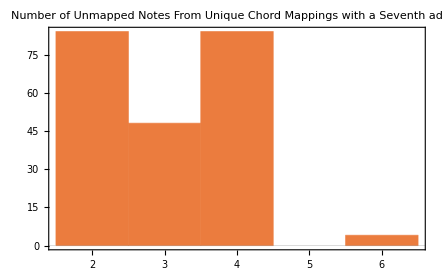

```mathematica
proofOfNoUniqueSeventh=Table[NotesLeftfromS[x,y,z], {x, 1,maxIndex-2}, {y, x+1, maxIndex-1}, {z, y+1, maxIndex}] //Flatten[#, 2]&;
Histogram[Length/@proofOfNoUniqueSeventh⟦1;;Length[proofOfNoUniqueSeventh]⟧,PlotTheme->"Scientific", PlotLabel->HoldForm[Number of Unmapped Notes From Unique Chord Mappings with a Seventh added] ]
```

Thus one can see that the mappings to the seventh fail to provide complete coverage, and that the unique mappings give a similar distribution (just rescaled by 1/6), just removing the five and 8 remaining mappings from (A,A,A) and (A, A, B) style mappings.

### Other Consistent Mappings

When applying this to the other potential mappings one gets the following minima number of non-mapped notes.

```mathematica
dSecondRule[s_]:={Flatten[NoNeut[s]], ChrS⟦DimSecond[s]⟧}
secondRule[s_]:={Flatten[NoNeut[s]], ChrS⟦Second[s]⟧}
dThirdRule[s_]:={Flatten[NoNeut[s]], ChrS⟦DimThird[s]⟧}
fourthRule[s_]:={Flatten[NoNeut[s]], ChrS⟦Fourth[s]⟧}
dFifthRule[s_]:={Flatten[NoNeut[s]], ChrS⟦DimFifth[s]⟧}
dSixthRule[s_]:={Flatten[NoNeut[s]], ChrS⟦DimSixth[s]⟧}
sixthRule[s_]:={Flatten[NoNeut[s]], ChrS⟦Sixth[s]⟧}
dSeventhRule[s_]:={Flatten[NoNeut[s]], ChrS⟦DimSeventh[s]⟧}
notesLeftfromd2[b1_, b2_, b3_]:=Complement[ChrS, Flatten[{dSecondRule[b1], dSecondRule[b2], dSecondRule[b3]}]]
notesLeftfrom2[b1_, b2_, b3_]:=Complement[ChrS, Flatten[{secondRule[b1], secondRule[b2], secondRule[b3]}]];
notesLeftfromd3[b1_, b2_, b3_]:=Complement[ChrS, Flatten[{dThirdRule[b1], dThirdRule[b2], dThirdRule[b3]}]];
notesLeftfrom4[b1_, b2_, b3_]:=Complement[ChrS, Flatten[{fourthRule[b1], fourthRule[b2], fourthRule[b3]}]];
notesLeftfromd5[b1_, b2_, b3_]:=Complement[ChrS, Flatten[{dFifthRule[b1], dFifthRule[b2], dFifthRule[b3]}]];
notesLeftfromd6[b1_, b2_, b3_]:=Complement[ChrS, Flatten[{dSixthRule[b1], dSixthRule[b2], dSixthRule[b3]}]];
notesLeftfrom6[b1_, b2_, b3_]:=Complement[ChrS, Flatten[{sixthRule[b1], sixthRule[b2], sixthRule[b3]}]];
notesLeftfromd27[b1_, b2_, b3_]:=Complement[ChrS, Flatten[{dSeventhRule[b1], dSeventhRule[b2], dSeventhRule[b3]}]];
dSeconddata=Flatten[Array[notesLeftfromd2, {12, 12,12}],2];
seconddata=Flatten[Array[notesLeftfrom2, {12, 12, 12}], 2];
d3data=Flatten[Array[notesLeftfromd3, {12, 12, 12}], 2];
fourthdata=Flatten[Array[notesLeftfrom4, {12, 12, 12}], 2];
d5data=Flatten[Array[notesLeftfromd5, {12, 12, 12}],2];
d6data=Flatten[Array[notesLeftfromd6, {12, 12, 12}], 2];
sixthdata=Flatten[Array[notesLeftfrom6, {12, 12, 12}],2];
d7data=Flatten[Array[notesLeftfromd27, {12, 12, 12}], 2];

PieChart[Counts@{Min[Length/@seconddata⟦1;;Length[seconddata]⟧],Min[Length/@d3data⟦1;;Length[d3data]⟧], Min[Length/@fourthdata⟦1;;Length[fourthdata]⟧], Min[Length/@d5data⟦1;;Length[d5data]⟧],Min[Length/@d6data⟦1;;Length[d6data]⟧],Min[Length/@sixthdata⟦1;;Length[sixthdata]⟧], Min[Length/@d7data⟦1;;Length[d7data]⟧],Min[Length/@Seventhdata⟦1;;Length[Seventhdata]⟧], Min[Length/@dSeconddata⟦1;;Length[dSeconddata]⟧]}, PlotLabel->"Minimum Number of Uncovered Notes by each Potential Mapping", ChartLabels->{"2 Remaining Notes", "1 Remaining Note"}]
```

-Graphics-

Thus, there is no mapping that follows the same rule for all three neutrinos that would be a bijection. Thus the neutrinos do not act as expected to properly fit in the model, just as massive neutrinos are a problem for the standard model.

### Inconsistent Mappings and Feynman Music

Thus, we again consider the above mentioned mappings (d7, d7, 2) and (6,6, d3). When considering the indices, one can see that all of the initial mappings must have the same format, three base notes in a sequence, thus it follows that these mapping options hold for all candidates. Then, choosing to use the d7, d7, d2 mapping (to preserve the 6ths for the anti-particles) and applying the unique choice to the tau-neutrino as it is expected to be significantly heavier than the other two flavor states. Choosing middle C as the base note for the Up quark and increasing from that point the mapping becomes (where we go to three gluons to emphasize the connection to the 3 colors). 
Particle | Note | Antiparticle | Note | Boson | Note
u | C | ū | A | γ | (G, A♭, A)
d | E | d̄ | C | H^0 | (D, E♭, F♯, A)
c | D♭ | c̄ | B♭ | Z^0 | (B♭, B, E♭)
s | F | s̄ | D♭ | W^+ | (B, C, E)
t | D | t̄ | B | W^- | (A, B♭, D)
b | F♯ | b̄ | D | g_1 | (C, E) 
e^- | G | e^+ | E | g_2 | (D♭, F)
μ^- | A♭ | μ^+ | F | g_3 | (D, F♯)
τ^- | A | τ^+ | F♯ | - | -
ν_e | B♭ | (ν̄)_e | G | - | -
ν_μ | B | (ν̄)_μ | A♭ | - | -
ν_τ | E♭ | (ν̄)_τ | E♭ | - | -

Now, consider again the above Feynman diagrams, and one finds that the new musical equivalent is:

```mathematica
-Graphics--Graphics-
```

```mathematica
eantieinteraction1=Sound[{Gn[3], En[3]}, 6]+ Pause[1]+{EmitSound[Gn[6]]+EmitSound[Gs[6]]+EmitSound[An[6]]}+Pause[1]+ Sound[{Gn[3], En[3]}, 6];
Button["Electron Positron Interaction", eantieinteraction1]
```

Electron Positron Interaction

```mathematica
higgsDecay1=EmitSound[Cn]+EmitSound[En]+Pause[1]+EmitSound[Cs]+EmitSound[Fn]+Pause[1]+Sound[{An[5], Dn[3], Bn[3]}, 6]+ Pause[1]+ EmitSound[Fs]+EmitSound[Dn]+EmitSound[Ds]+EmitSound[An]+Pause[1]+Sound[{Fs[4], Dn[3], Cs[2], As[0.5], As[0.5]}]+Pause[1]+EmitSound[Bn]+EmitSound[Cn]+EmitSound[En]+Pause[0.5]+EmitSound[An]+EmitSound[As]+EmitSound[Dn]+Pause[1]+Sound[{Gs[1], Gs[1], En[1], An[1]}];
Button["Higgs Boson Decay", higgsDecay1]
```

Higgs Boson Decay

## “Serialism” and Feynman Diagrams

Schoenberg proposed a system of composing music in a quasi-mathematical application. Schoenberg defined a base line, and then constructed a matrix of allowable future lines based on rotations and deformations of the original line. This form of music via deformation can be applied to the Feynman diagrams, as they are also to be defined by grouping with comparable deformations. Further, Schoenberg and his followers made a conscious choice to avoid the use of key, which is in line with the inconsistent mapping above and choice of diminished 7th over the proper minor  that would have been highlighted in the sixth.  However, while Schoenberg’s matrix relies on the base line being constructed from all twelve notes at least once, Feynman diagrams are usually not compatible with this component of Schoenberg and the Second Viennese School’s Project. (See “Style and Idea: Selected Writings of Arnold Schoenberg” 1975). 
	To this end, we define, for the electron positron interactions, a 12x7 matrix corresponding to the 12 rotations and deformations shown below.

(1)(2)The Base and Reflection: -Graphics-
(3)(4)Rotation by π and reflection: -Graphics-
(5)(6)Rotation to the right by π/2 and 3π/2: -Graphics-
(7)(8)Rotation to the right by π/2 and 3π/2 with a reflection: 
(9)Deformation: -Graphics-
(10) Deformation with reflection: -Graphics-
(11) Rotation to the right by π/2 of Deformation:-Graphics-
(12) Rotation by π/2 with a reflection of deformation: 
One can see that not all deformations or rotations of such have been shown. This is to limit the scope to 12 rows to show agreement with the Serialist project; however, it could be easily expanded to include all such transformations.

The Output music would be:

Which gives the matrix:

## Conclusion

In this essay, a novel method for the mapping of fermions on to the 12 tones of the chromatic scale has been presented along with an integration of a modified version of Serialism in music. The next logical steps of this project would be a forwards and backwards automatic conversion from music to Feynman diagrams and Feynman diagrams to music. To this end, the opening three bars of “Eine Kleine Nachtmusik” by Motzart would have the following Feynman diagram, where only one of the possible diagrams is shown.

## Initialization Cells

```mathematica
An[n_]:=SoundNote["A", n, "Violin"]
Bn[m_]:=SoundNote["B", m, "Violin"]
As[m1_]:=SoundNote["ASharp", m1, "Violin"]
Cn[m2_]:=SoundNote["C", m2, "Violin"]
Cs[m3_]:=SoundNote["CSharp", m3, "Violin"]
Dn[m4_]:=SoundNote["D", m4, "Violin"]
Ds[m5_]:=SoundNote["DSharp", m5, "Violin"]
En[m6_]:=SoundNote["E", m6, "Violin"]
Fn[m7_]:=SoundNote["F", m7, "Violin"]
Fs[m8_]:=SoundNote["FSharp", m8, "Violin"]
Gn[m9_]:=SoundNote["G", m9, "Violin"]
Gs[m10_]:=SoundNote["GSharp", m10, "Violin"]
```

```mathematica
ChrS:={An, As, Bn, Cn, Cs, Dn, Ds, En, Fn, Fs, Gn, Gs} (*Chromatic Scale*)
DimSecond[a_]:=If[a<12, a+1, 1];
Second[b_]:=If[b<11, b+2,   1+Mod[b+1, 12]];
DimThird[c_]:=If[c<10, c+3, 1+Mod[c+2, 12]];
Third[d_]:=If[d<9, d+4, 1+Mod[d+3, 12]];
Fourth[e_]:=If[e<8, e+5, 1+Mod[e+4, 12]];
DimFifth[f_]:=If[f<7, f+6, 1+Mod[f+5, 12]];
Fifth[g_]:=If[g<6, g+7, 1+Mod[g+6, 12]];
DimSixth[h_]:=If[h<5, h+8, 1+Mod[h+7, 12]];
Sixth[i_]:=If[i<4, i+9, 1+Mod[i+8, 12]];
DimSeventh[j_]:=If[j<3, j+10, 1+Mod[j+9, 12]];
Seventh[k_]:=If[k<2, k+11, 1+Mod[k+10, 12]];
```